```mathematica
f[n_,x_]:=HermiteH[n,x]/Sqrt[2^n n!]*Exp[-x^2/2];
```

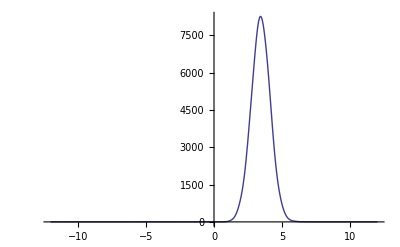

```mathematica
Plot[Abs[G[0.2]]^2,{x,-12,12},PlotRange->All]
```

```mathematica
Animate[Plot[{Abs[G[b]]^2},{x,-7,7},PlotRange->All],{b,0,2}]
```

```mathematica
a[b_]:=1*Exp[I*b*Pi];g=Simplify[Sum[a[b]^n/Sqrt[n!] f[n,x],{n,0,20}]];
```

```mathematica
G[B_]:=g/.b->B//N
```

```mathematica
1/Sqrt[900]
```

1/30